```mathematica
kHz = 10^3;
Hz=1;
ωz = 2*π*710*kHz;
```

## Two ions - mixed species

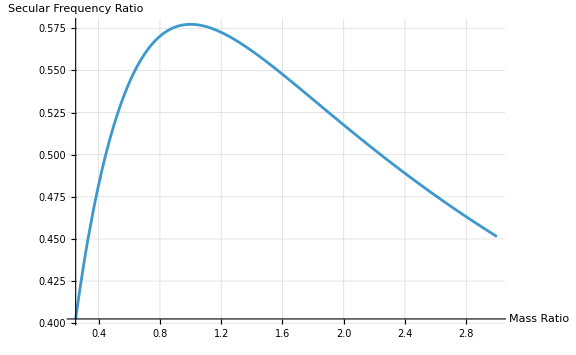

```mathematica
Ωm[μ_, ωz_] := Sqrt[(1+μ-Sqrt[1-μ+μ^2])/μ]*ωz
Ωp[μ_, ωz_] := Sqrt[(1+μ+Sqrt[1-μ+μ^2])/μ]*ωz
Plot[Ωm[μ, ωz]/Ωp[μ, ωz], {μ, 0.25,3},
AxesLabel->{Style["Mass Ratio", 16], Style["Secular Frequency Ratio", 16]},
GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
```

## Three ions - mixed species (2 bright, 1 dark)

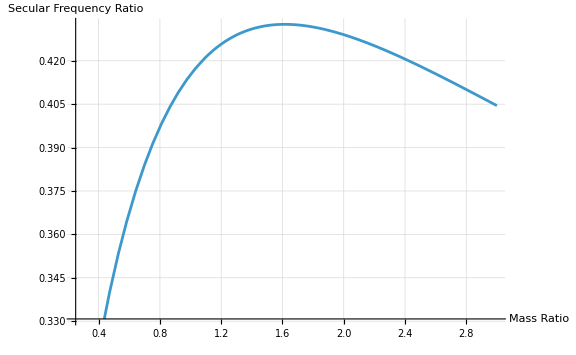

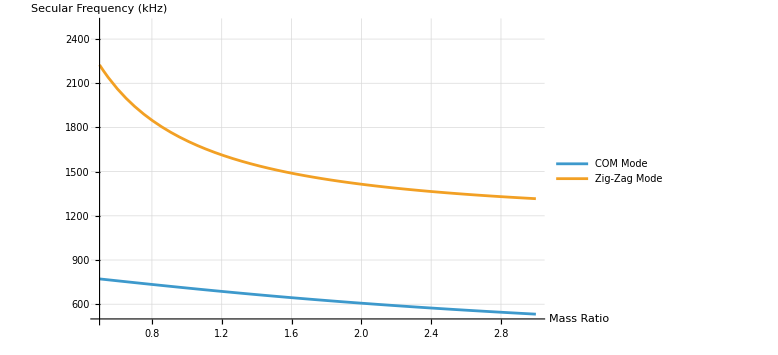

```mathematica
η1[μ_, ωz_]:= ωz*Sqrt[13/10+1/(10μ)(21-Sqrt[441-34μ+169 μ^2])];
η3[μ_, ωz_]:= ωz*Sqrt[13/10+1/(10μ)(21+Sqrt[441-34μ+169 μ^2])];
Plot[η1[μ, ωz]/η3[μ, ωz], {μ,0.25,3},
AxesLabel->{Style["Mass Ratio", 16], Style["Secular Frequency Ratio", 16]},
GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
MixedModesSec = Plot[{η1[μ, ωz]/(2*π*kHz), η3[μ, ωz]/(2*π*kHz)}, {μ,0.5,3}, 
AxesLabel->{Style["Mass Ratio", 16], Style["Secular Frequency (kHz)", 16]}, PlotLegends->{"COM Mode", "Zig-Zag Mode"},
PlotRange->{500,2500},  GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
(*Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\mixedModeSec.svg", MixedModesSec];*)
```

```mathematica
N[{1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1]+1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1]}/.{μ->36/40}]
```

{1.18217}

```mathematica
{1.1821733886544934}
N[2/Sqrt[3]]
```

{1.18217}

1.1547

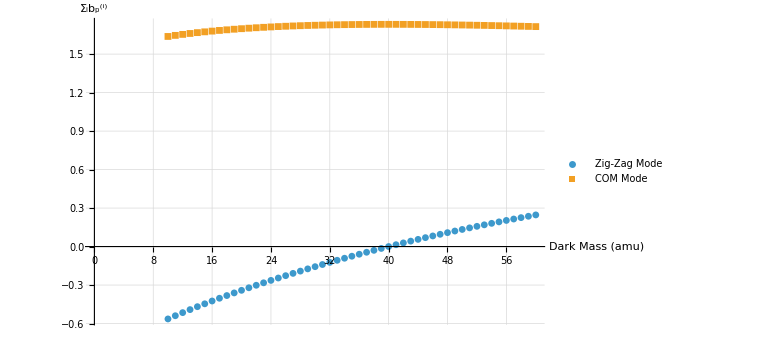

```mathematica
ComVec[μ_]:= {1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1],(Sqrt[μ]/8(13-5*η1[μ,1]^2))/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1],1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1]};
ZigVec[μ_]:= {1/Sqrt[1+(Sqrt[μ]/8(13-5*η3[μ,1]^2))^2+1],(Sqrt[μ]/8(13-5*η3[μ, 1]^2))/Sqrt[1+(Sqrt[μ]/8(13-5*η3[μ,1]^2))^2+1],1/Sqrt[1+(Sqrt[μ]/8(13-5*η3[μ,1]^2))^2+1]};
masses = Range[10,60];
modeCoupling = ZigVec[masses/40];
modeCouplingDarkMass = ListPlot[{Thread[{masses, Total[ZigVec[masses/40]]}], Thread[{masses, Total[ComVec[masses/40]]}]},
AxesLabel->{Style["Dark Mass (amu)", 16], Style["Σ_ib_p^(i)", 16]}, PlotLegends->{"Zig-Zag Mode", "COM Mode"}, 
PlotMarkers->{Automatic, Small}, GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\modeCouplingDarkMass.svg", modeCouplingDarkMass];
```

```mathematica
N[Total[ZigVec[10/40]]]
```

-0.564124

## Determine mass

```mathematica
(*All masses are in units of amu*)
mCa = 39.962590863;
mElectron = 0.0005486; 
mCaIon = mCa - mElectron; 
mH = 1.007825032; 
mHClAcc = 35.97555342; (*Grant's Number*)
mCl35 = 34.968852;
mHCl35 = mH + mCl35 - mElectron; 
mCl37 = 36.9659023;
mHCl37 = 2*mH + mCl37 - mElectron;
```

```mathematica
mHCl35
```

35.9761

```mathematica
(*Allen Dev Parameters*)
comMode = 2*π*732.484*kHz;
calibrationCOMDetuning = -11*Hz;
rollingMeanCOMDetuning = 15*Hz; 
comModeDetuning = 2*π*(calibrationCOMDetuning + rollingMeanCOMDetuning - 238);
zigMode = 2*π*1797.9729*kHz;
calibrationZZDetuning = -2*Hz;
rollingMeanZZDetuning = 3.14*Hz; 
zigModeDetuning = 2*π*(calibrationZZDetuning + rollingMeanZZDetuning - 281);
```

### Use ratio of secular frequencies to get mass

```mathematica
η1[μ_, ωz_]:= ωz*Sqrt[13/10+1/(10μ)(21-Sqrt[441-34μ+169 μ^2])];
η3[μ_, ωz_]:= ωz*Sqrt[13/10+1/(10μ)(21+Sqrt[441-34μ+169 μ^2])];
sols = FullSimplify[Solve[η1[μ, ωz]/η3[μ, ωz]== R, μ]];
f = sols[[1]][[1]][[2]]/.{R->ω1/ω3};
σμ = FullSimplify[Sqrt[(D[f, ω1])^2 Subscript[σ, ω1]^2+(D[f, ω3])^2 Subscript[σ, ω3]^2+2*D[f, ω1]*D[f, ω3]*0]];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
mHClPred = mCaIon* (sols[[1]][[1]][[2]]/.{R->(comMode+comModeDetuning)/(zigMode+zigModeDetuning)})
σμ = FullSimplify[Sqrt[(D[f, ω1])^2 Subscript[σ, ω1]^2+(D[f, ω3])^2 Subscript[σ, ω3]^2+2*D[f, ω1]*D[f, ω3]*0]];
mCaIon*σμ/.{ω1->2π*(comMode+comModeDetuning), ω3->2*π*(zigMode+zigModeDetuning), Subscript[σ, ω1]->0.98*2*π,Subscript[σ, ω3]->2.3*2*π}
(mHClPred - mHCl35)/mElectron
```

35.977

0.0000533611

1.59108

```mathematica
mCaIon * sols[[1]][[1]][[2]]/.{R->(comMode+comModeDetuning)/(zigMode+zigModeDetuning)}
```

36.0052

```mathematica
ω11 = comMode+comModeDetuning;
ω33= zigMode+zigModeDetuning;
mCaIon * FullSimplify[NSolve[η1[μ, ωz]/η3[μ, ωz]== ω11/ω33, μ]][[2]][[1]][[2]]
```

36.0076

### Use single ion secular frequencies to make mass estimate

```mathematica
ωzSingle = 2*π*710.8*kHz;
```

#### Axial COM

```mathematica
solsCOM = FullSimplify[Solve[η1[μ, ωz]/ωz== R, μ]];
mCaAmu * (solsCOM[[1]][[1]][[2]]/.{R->(comMode+comModeDetuning)/ωzSingle})
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.821468 mCaAmu

#### Axial ZZ

```mathematica
solsZZ = FullSimplify[Solve[η3[μ, ωz]/ωz== R, μ]];
mCaAmu * (solsZZ[[1]][[1]][[2]]/.{R->(zigMode+zigModeDetuning)/ωzSingle})
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

0.866846 mCaAmu

```mathematica
solsCOM/.{R->(zigMode+zigModeDetuning)/ωzSingle}
```

{{μ→0.866972}}

```mathematica
η1[μ, ωz+δ]/η3[μ, ωz+δ]
```

(√(13/10+(21-√(441-34 μ+169 μ^2))/(10 μ)))/(√(13/10+(21+√(441-34 μ+169 μ^2))/(10 μ)))